# Evaluating the Value of π

Evaluate the value of π  using four Power Series

Dhruv Thanawala, Jun. 24,  2018

Create a function that evaluate the Power Series for calculating the value of π. There are many power series to evaluate the value of π. Here I discussed four series. 1) Madhva-Leibniz Series 2) Ramanujan-Sato Series 3) Bailey–Borwein–Plouffe Series 4) Wallis Series. Out of those series some of them converges very fast and some of them very slow. Below is the discussion of these Power Series.

Clear all the data of the functions and variables

```mathematica
ClearAll[ComputePi,PiApproximation,i,j,n,k,piApproximation]
```

General function to compute π

```mathematica
ComputePi[n_,j_]:=Module[{i=0},
For[i=1,i≤n,i++,
piApproximation[i,j] =PiApproximation[i]
]
]
```

## Madhva–Leibniz Series

In Mathematics, the Madhva-Leibniz Series states that,
π/4=1-1/3+1/5-1/7+1/9-...

So, the above series is the expansion of the inverse tangent series .  The Indian mathematician Madhava discovered this series in 14th century. In 1676, Leibniz publish this specific case of inverse tangent series. After that, Gregory gave the expansion of the inverse tangent series, which is given by,

Arctan x = x-x/3+x/5-x/7+x/9-...

Up to 10 correct decimal the Leibniz's formula converges extremely slowly. The reason behind that is, 1/(2k +1)<10^-10for k > 5*10^9-1/2. But still this formula can be used to calculate π to high precision.

Pi Approximation function for Leibniz Series

```mathematica
PiApproximation[n_]:=4.0*∑_(k=1)^n (-1)^(k+1)/(2.*k-1);
ComputePi[1000,1]
```

Plot for Leibniz series π and actual π

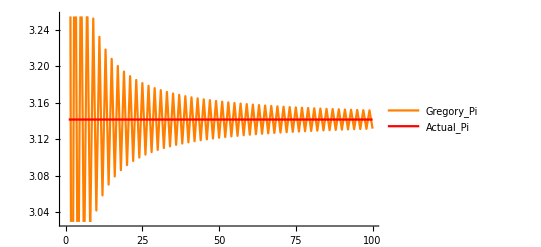

```mathematica
Show[ListLinePlot[Table[piApproximation[p,1],{p,100}],PlotLegends->{"Gregory_Pi"},PlotStyle->{Orange}],Plot[0*x+Pi,{x,1,100},PlotLegends->{"Actual_Pi"},PlotStyle->{Red}]]
```

## Ramanujan-Sato Seeries

In mathematics, a Ramanujan–Sato series generalizes Ramanujan’s pi formulas such as,

1/π=(2 √2)/99^2  ∑_(k=0)^n ((4.0*k)!)/(k!)^4(26390*k+1103)/396^(4*k)

In November, 1985, R. William Gosper, Jr. used one of the Ramanujan’s series to calculate 17,526,100 digits of π, which was the world record at that time.  In 1987, Jonathan and Peter Borwein succeeded in proving all 17 of Ramanujan’s series for 1/π.

Pi Approximation function for Ramanujan and Sato Series

```mathematica
PiApproximation[n_]:= 99^2/(2 √2∑_(k=0)^n ((4.0*k)!)/(k!)^4(26390*k+1103)/396^(4*k));
ComputePi[1000,2]
```

Plot for Ramanujan series π and actual π

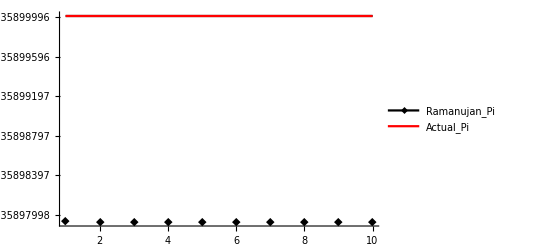

```mathematica
Show[ListLinePlot[Table[piApproximation[p,2],{p,10}],PlotLegends->{"Ramanujan_Pi"},PlotStyle->{Black}, PlotMarkers->{"◆"}],Plot[0*x+Pi,{x,1,10},PlotLegends->{"Actual_Pi"},PlotStyle->{Red}],PlotRange -> Automatic]
```

## Bailey–Borwein–Plouffe formula (BBP formula)

The Bailey–Borwein–Plouffe formula (BBP formula) is for computing the n^thbinary digit of the mathematical constant π using base-16 representation. It is a spigot algorithm.This formula is interesting because it computes the n^thdigit of π without calculating all the preceding n-1 digits. The BBP is a summation-style formula which was discovered in 1995 by Simon Plouffe and was named after the authors of the article in which the formula was published, David H. Bailey, Peter Borwein, and Plouffe. The formula is,

π  =  ∑_(k=0)^∞ 1/16^k(4.0/(8*k+1)-2.0/(8*k+4)-1.0/(8*k+5)-1.0/(8*k+6))

Pi Approximation function for BBP Formula

```mathematica
PiApproximation[n_] :=∑_(k=0)^n 1/16^k(4.0/(8*k+1)-2.0/(8*k+4)-1.0/(8*k+5)-1.0/(8*k+6));
ComputePi[1000,3]
```

Plot for BBP series π and actual π

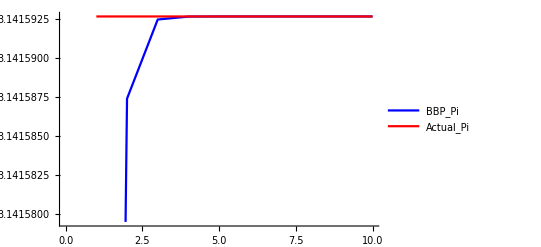

```mathematica
Show[ListLinePlot[Table[piApproximation[p,3],{p,10}],PlotLegends->{"BBP_Pi"},PlotStyle->{Blue}],Plot[0*x+Pi,{x,1,10},PlotLegends->{"Actual_Pi"},PlotStyle->{Red}]]
```

## Wallis Series

In 1655 by John Wallis discovered the Wallis product which states that,

∏_(n=1)^∞ ((2n)/(2n-1).(2n)/(2n+1)) = π/2

Wallis derived this infinite product by examining ∫_0^π Sin xⅆx for even and odd values of n, and noting that for large n, increasing n by 1 results in a change that becomes ever smaller as n increases.

Proof:

(Sin x)/x=  ∏_(n=1)^∞ (1-(x^2 n^2)/π^2)
Let x  = π/2;
⇒π/2= ∏_(n=1)^∞ (4 n^2)/(4 n^2-1)

Pi Approximation function for Wallis Series

```mathematica
PiApproximation[n_] := 2* ∏_(k=1)^n (2.0*k)^2/(4.0*k^2-1)
ComputePi[1000,4]
```

Plot for Wallis series π and actual π

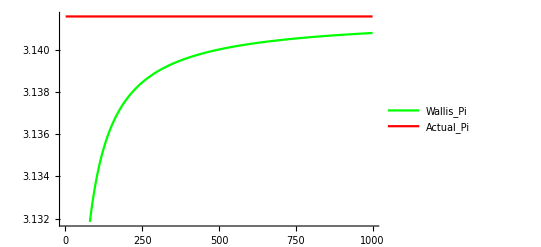

```mathematica
Show[ListLinePlot[Table[piApproximation[p,4],{p,1000}],PlotLegends->{"Wallis_Pi"},PlotStyle->{Green}],
Plot[0*x+Pi,{x,1,1000},PlotLegends->{"Actual_Pi"},PlotStyle->{Red}],PlotRange->Automatic]
```

## Plot comparison

So, the plot indicates that the Ramanujan-Sato and BBP formula converges fast as compare to Gregory-Leibniz series and Wallis Product series.

Plot comparison of all series

```mathematica
Animate[Show[ListLinePlot[Table[piApproximation[p,1],{p,n}],PlotLegends->{"Gregory_Pi"},PlotStyle->{Orange}],
ListLinePlot[Table[piApproximation[p,2],{p,n}],PlotLegends->{"Ramanujan_Pi"},PlotStyle->{Black}],
ListLinePlot[Table[piApproximation[p,3],{p,n}],PlotLegends->{"BBP_Pi"},PlotStyle->{Blue}],
ListLinePlot[Table[piApproximation[p,4],{p,n}],PlotLegends->{"Wallis_Pi"},PlotStyle->{Green}],
Plot[0*x+Pi,{x,1,n},PlotLegends->{"Actual_Pi"},PlotStyle->{Red}],
PlotRange->Automatic],{n,1,1000}]
```

## Author contact information

Dhruv Thanawala

twdhruv@gmail.com

## Further Explorations

Taylor Series
Newton polynomial